```mathematica
If[$MachineName!="iapetus",SetDirectory["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/"],SetDirectory["/export/data1/caplarn/Documents/Small/Eurovision2016"];]
```

/home/caplarn/Documents/Astrodataiscool/Eurovision2017

```mathematica
LaunchKernels[4]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
kernels=ParallelTable[$KernelID->i,{i,$KernelCount}];
SetSharedVariable[kernels];SetSharedVariable[currentNumber]
currentNumber=ConstantArray[0,Length@kernels];
```

## Preparing cities

```mathematica
(*worldcities=Flatten[Import["GlobalAirportDatabase.txt","CSV"],1];
worldcitiesSplit=Map[StringSplit[#,":"]&,worldcities];*)
```

```mathematica
city2=Import["worldcitiespop.txt","CSV"];
```

```mathematica
city2withpopulation=Select[city2,#[[5]]>10000&];
```

```mathematica
Length[city2]
```

3173959

```mathematica
Length[city2withpopulation]
```

25077

```mathematica
ShortName={"se","ge","au","al","be","mn","fi","az","po","gr","pl","md","is","cz","cy","ar","si","lv","rs","au","mk","mt","ro","ne","hu","de","ie","sm","hr","no","ch","by","bl","lt","ee","il","ua","fr","de","it","es","gb"};
LongName={"SWEDEN","GEORGIA","AUSTRALIA","ALBANIA","BELGIUM","MONTENEGRO","FINLAND","AZERBAIJAN","PORTUGAL","GREECE","POLAND","MOLDOVA","ICELAND","CZECH REPUBLIC","CYPRUS","ARMENIA","SLOVENIA","LATVIA","SERBIA","AUSTRIA","MACEDONIA","MALTA","ROMANIA","NETHERLANDS","HUNGARY","DENMARK","IRELAND","SAN MARINO","CROATIA","NORWAY","SWITZERLAND","BELARUS","BULGARIA","LITHUANIA","ESTONIA","ISRAEL","UKRAINE","FRANCE","GERMANY","ITALY","SPAIN","UK"};
LongNameForImport=LongName;
LocalName={"Sverige","Sakartvelo","AUSTRALIA","Shqiperi","Belgie","crna","SUOMI","Azerbaycan","Portuguesa","Hellas","Polska","MOLDOVA","Island","ceska","Cipros","Hayastan","Slovenia","Latvija","SRBIJA","Osterreich","MAKEDONIJA","MALTA","Romania","Nederland","Magyarorszag","Danmark","IRELAND","MARINO","HRVATSKA","Norge","Schweiz","Bielarus","Balgariya","Lietuva","Eesti","Yisrael","Ukraina","francaise","Deutschland","Italia","Espana","UK"};
```

```mathematica
Length[ShortName]
Length[LongName]
Length[LocalName]
```

42

42

43

```mathematica
{ShortName,LongName}//Transpose
```

{{se,SWEDEN},{ge,GEORGIA},{au,AUSTRALIA},{al,ALBANIA},{be,BELGIUM},{mn,MONTENEGRO},{fi,FINLAND},{az,AZERBAIJAN},{po,PORTUGAL},{gr,GREECE},{pl,POLAND},{md,MOLDOVA},{is,ICELAND},{cz,CZECH REPUBLIC},{cy,CYPRUS},{ar,ARMENIA},{si,SLOVENIA},{lv,LATVIA},{rs,SERBIA},{au,AUSTRIA},{mk,MACEDONIA},{mt,MALTA},{ro,ROMANIA},{ne,NETHERLANDS},{hu,HUNGARY},{de,DENMARK},{ie,IRELAND},{sm,SAN MARINO},{hr,CROATIA},{no,NORWAY},{ch,SWITZERLAND},{by,BELARUS},{bl,BULGARIA},{lt,LITHUANIA},{ee,ESTONIA},{il,ISRAEL},{ua,UKRAINE},{fr,FRANCE},{de,GERMANY},{it,ITALY},{es,SPAIN},{gb,UK}}

```mathematica
{LongName,LocalName}//Transpose
```

{{SWEDEN,Sverige},{GEORGIA,Sakartvelo},{AUSTRALIA,AUSTRALIA},{ALBANIA,Shqiperi},{BELGIUM,Belgie},{MONTENEGRO,crna},{FINLAND,SUOMI},{AZERBAIJAN,Azerbaycan},{PORTUGAL,Portuguesa},{GREECE,Hellas},{POLAND,Polska},{MOLDOVA,MOLDOVA},{ICELAND,Island},{CZECH REPUBLIC,ceska},{CYPRUS,Cipros},{ARMENIA,Hayastan},{SLOVENIA,Slovenia},{LATVIA,Latvija},{SERBIA,SRBIJA},{AUSTRIA,Osterreich},{MACEDONIA,MAKEDONIJA},{MALTA,MALTA},{ROMANIA,Romania},{NETHERLANDS,Nederland},{HUNGARY,Magyarorszag},{DENMARK,Danmark},{IRELAND,IRELAND},{SAN MARINO,MARINO},{CROATIA,HRVATSKA},{NORWAY,Norge},{SWITZERLAND,Schweiz},{BELARUS,Bielarus},{BULGARIA,Balgariya},{LITHUANIA,Lietuva},{ESTONIA,Eesti},{ISRAEL,Yisrael},{UKRAINE,Ukraina},{FRANCE,francaise},{GERMANY,Deutschland},{ITALY,Italia},{SPAIN,Espana},{UK,UK}}

```mathematica
If[$MachineName!="iapetus",SetDirectory["~/Documents/Astrodataiscool/Eurovision2016/Cities"],SetDirectory["/export/data1/caplarn/Documents/Small/Eurovision2016/Cities"];]
```

/home/caplarn/Documents/Astrodataiscool/Eurovision2016/Cities

```mathematica
Table[CityFromCountry=Reverse[SortBy[Select[city2withpopulation,#[[1]]==ShortName[[i]]&],#[[5]]&]];CityFromCountry100=If[Length[CityFromCountry]>100,CityFromCountry[[1;;100]],CityFromCountry];
Save[LongName[[i]],CityFromCountry100];,{i,Length[ShortName]}];
```

```mathematica
SearchNames=Table[Join[{LongName[[i]]},{LocalName[[i]]},CityFromCountry=Get[LongName[[i]]];CityFromCountry[[All,3]]],{i,Length[LongName]}];
```

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Select::argb will be suppressed during this calculation.

```mathematica
SearchNames[[25]]
```

{HUNGARY,Magyarorszag,Budapest,Debrecen,Miskolc,Szeged,Pécs,Gyor,Nyíregyháza,Kecskemét,Székesfehérvár,Szombathely,Szolnok,Tatabánya,Kaposvár,Békéscsaba,Zalaegerszeg,Veszprém,Érd,Eger,Sopron,Dunaújváros,Nagykanizsa,Hodmezovasarhely,Salgótarján,Cegléd,Ózd,Baja,Szekszárd,Vác,Pápa,Gyöngyös,Kazincbarcika,Godollo,Gyula,Hajdúböszörmény,Kiskunfélegyháza,Ajka,Orosháza,Szentes,Mosonmagyaróvár,Dunakeszi,Kiskunhalas,Esztergom,Jászberény,Komló,Nagykoros,Makó,Budaörs,Szigetszentmiklós,Tata,Szentendre,Hajdúszoboszló,Siófok,Törökszentmiklós,Hatvan,Karcag,Gyál,Monor,Keszthely,Várpalota,Békés,Dombóvár,Paks,Oroszlány,Komárom,Vecsés,Mezotur,Mátészalka,Mohács,Csongrád,Kalocsa,Kisvárda,Szarvas,Sátoraljaújhely,Hajdúnánás,Balmazújváros,Mezokovesd,Tapolca,Százhalombatta,Balassagyarmat,Tiszaújváros,Dunaharaszti,Fót,Dabas,Abony,Berettyóújfalu,Püspökladány,Göd,Sárvár,Gyomaendrod,Kiskoros,Pomáz,Mór,Sárospatak,Bátonyterenye,Bonyhád,Gyomro,Tiszavasvári,Újfehértó,Nyírbátor,Sárbogárd}

## Prep analysis

```mathematica
If[$MachineName!="iapetus",SetDirectory["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data/"],SetDirectory["/export/data1/caplarn/Documents/Small/Eurovision2016"];]
```

/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data

```mathematica
hashtags={"#SWE","#GEO", "#AUS","#ALB", "#BEL", "#MNE", "#FIN", "#AZE", "#POR", "#GRE", "#POL", "#MDA", "#ISL", "#CZE", "#CYP","#ARM","#SLO","#LAT"}
```

{#SWE,#GEO,#AUS,#ALB,#BEL,#MNE,#FIN,#AZE,#POR,#GRE,#POL,#MDA,#ISL,#CZE,#CYP,#ARM,#SLO,#LAT}

```mathematica
(*should be sui*)
hashtags2={"#SRB","#AUT", "#MKD", "#MLT", "#ROM", "#NED", "#HUN", "#DEN", "#IRL", "#SMR", "#CRO", "#NOR", "#SUI", "#BLR", "#BUL","#LTU","#EST","#ISR"}
```

{#SRB,#AUT,#MKD,#MLT,#ROM,#NED,#HUN,#DEN,#IRL,#SMR,#CRO,#NOR,#SUI,#BLR,#BUL,#LTU,#EST,#ISR}

```mathematica
hashtagsall=Join[hashtags,hashtags2]
```

{#SWE,#GEO,#AUS,#ALB,#BEL,#MNE,#FIN,#AZE,#POR,#GRE,#POL,#MDA,#ISL,#CZE,#CYP,#ARM,#SLO,#LAT,#SRB,#AUT,#MKD,#MLT,#ROM,#NED,#HUN,#DEN,#IRL,#SMR,#CRO,#NOR,#SUI,#BLR,#BUL,#LTU,#EST,#ISR}

```mathematica
If[$MachineName!="iapetus",SetDirectory["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data"],SetDirectory["/export/data1/caplarn/Documents/Small/Eurovision2016/TwitterData"];]
```

/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data

```mathematica
RawTwitterData=Table[Import[ToLowerCase[StringDrop[hashtags[[i]],1]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterData=Table[{StringJoin[Table[RawTwitterData[[j,i]],{i,Length[RawTwitterData[[j]]]}]]},{j,Length[RawTwitterData]}];,j]
```

```mathematica
RawTwitterDataEurovisionHashtag=Table[Import[ToString[LongNameForImport[[i]]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterDataEurovisionHashtag=Table[{StringJoin[Table[RawTwitterDataEurovisionHashtag[[j,i]],{i,Length[RawTwitterDataEurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterDataEurovisionHashtag]}];,j]
```

```mathematica
RawTwitterData=Table[{RawTwitterData[[i,1]]<>RawTwitterDataEurovisionHashtag[[i,1]]},{i,Length[RawTwitterDataEurovisionHashtag]}];
```

```mathematica
(*2nd*)
```

```mathematica
RawTwitterData2=Table[Import[ToLowerCase[StringDrop[hashtags2[[i]],1]]<>".txt","Data"],{i,18}];
Monitor[RawTwitterData2=Table[{StringJoin[Table[RawTwitterData2[[j,i]],{i,Length[RawTwitterData2[[j]]]}]]},{j,Length[RawTwitterData2]}];,j]
```

```mathematica
RawTwitterData2EurovisionHashtag=Table[Import[ToString[LongNameForImport[[i]]]<>".txt","Data"],{i,19,36}];
Monitor[RawTwitterData2EurovisionHashtag=Table[{StringJoin[Table[RawTwitterData2EurovisionHashtag[[j,i]],{i,Length[RawTwitterData2EurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterData2EurovisionHashtag]}];,j]
```

```mathematica
RawTwitterData2=Table[{RawTwitterData2[[i,1]]<>RawTwitterData2EurovisionHashtag[[i,1]]},{i,Length[RawTwitterData2EurovisionHashtag]}];
```

#### Analysis

```mathematica
SetDirectory["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data"]
```

/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data

```mathematica
f[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0];,i];
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2017,5,09,18,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReducedEurovisionAdded=Table[f[RawTwitterData[[j]]],{j,Length[RawTwitterData]}];,{i,j}]]
```

{1492.1,Null}

```mathematica
Save["DataReducedEurovisionAdded",DataReducedEurovisionAdded];
```

```mathematica
f2[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0],i]
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2016,5,11,18,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
(*needs to be done with full dataset*)
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReduced2EurovisionAdded=Table[f2[RawTwitterData2[[j]]],{j,Length[RawTwitterData2]}];,{i,j}]]
```

{1221.61,Null}

```mathematica
Save["DataReduced2EurovisionAdded",DataReduced2EurovisionAdded];
```

### Firing plots

```mathematica
SetDirectory[];
PlotOptions1={Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{25,FontFamily->"Helvetica"}};
fS=20;
pDisco[col_,testo_]={Graphics[{col,Thickness[0.1],Disk[{0.6,0.2},0.7]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
pRectangle[col_,testo_]={Graphics[{col,Thickness[0.1],Rectangle[{0,0}]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
linea[col_,ltype_,n_,t_,testo_]:={Graphics[{col,ltype,Opacity[n],Thickness[t],Line[{{0,-0.4},{1,-0.4}}]},ImageSize-> 40,AspectRatio-> 0.1],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
```

```mathematica
Colors={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255]};
Colors2={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255]};
```

```mathematica
SetDirectory["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/Data/"];
Get["DataReducedEurovisionAdded"];Get["DataReduced2EurovisionAdded"];(*This line because analyzed with wrong function, moved by 2 days*)
DataReduced2=DataReduced2EurovisionAdded;DataReduced=DataReducedEurovisionAdded;(*This line most of function use DataReduced*)
```

```mathematica
int=Table[Interpolation[{Table[i-1+0.01,{i,0,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{0,3.5,0.02}]}//Transpose],{j,Length[DataReducedEurovisionAdded]}];
intButNoInt=Table[{Table[i-1+0.01,{i,0,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{0,3.5,0.02}]}//Transpose,{j,Length[DataReducedEurovisionAdded]}];
TableOfMax=Table[Select[intButNoInt[[i]],#[[2]]==Max[intButNoInt[[i]]]&][[1]],{i,18}];
```

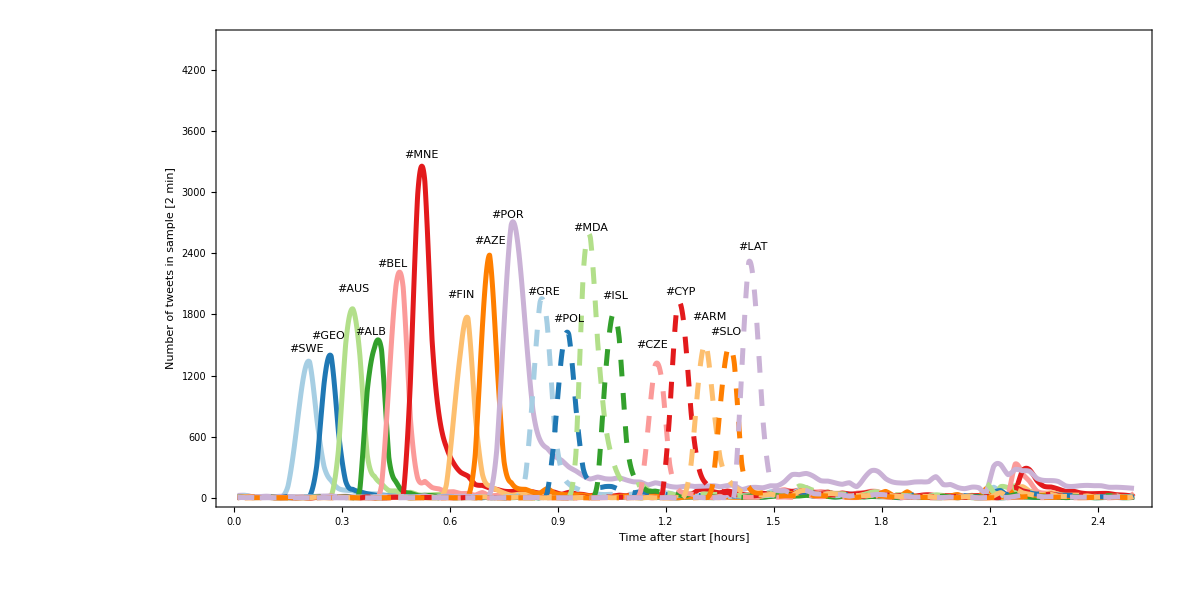

```mathematica
CustomOffset={{0,-20},{0,50},{+0.01,40},{0.00,10},{0.0,60},{+0.00,100},{-0.01,80},{0.01,-10},{0,-50},{0.02,-50},{0.01,0},{0.01,-50},{0.02,50},{0.00,50},{0.02,0},{0.02,100},{0.005,30},{0.02,0}};
SF1=Plot[{int[[1]][x],int[[2]][x],int[[3]][x],int[[4]][x],int[[5]][x],int[[6]][x],int[[7]][x],int[[8]][x],int[[9]][x],int[[10]][x],int[[11]][x],int[[12]][x],int[[13]][x],int[[14]][x],int[[15]][x],int[[16]][x],int[[17]][x],int[[18]][x]},{x,0.01,2.5},PlotRange->{{0,2.5},{0,4500}},ImageSize->1200,AspectRatio->1/2,PlotStyle->{{Thickness[0.003],RGBColor[166/255,206/255,227/255]},{Thickness[0.003],RGBColor[31/255,120/255,180/255]},{Thickness[0.003],RGBColor[178/255,223/255,138/255]},{Thickness[0.003],RGBColor[51/255,160/255,44/255]},{Thickness[0.003],RGBColor[251/255,154/255,153/255]},{Thickness[0.003],RGBColor[227/255,26/255,28/255]},{Thickness[0.003],RGBColor[253/255,191/255,111/255]},{Thickness[0.003],RGBColor[255/255,127/255,0/255]},{Thickness[0.003],RGBColor[202/255,178/255,214/255]},{Thickness[0.003],RGBColor[166/255,206/255,227/255],Dashing[0.01]},{Thickness[0.003],RGBColor[31/255,120/255,180/255],Dashing[0.01]},{Thickness[0.003],RGBColor[178/255,223/255,138/255],Dashing[0.01]},{Thickness[0.003],RGBColor[51/255,160/255,44/255],Dashing[0.01]},{Thickness[0.003],RGBColor[251/255,154/255,153/255],Dashing[0.01]},{Thickness[0.003],RGBColor[227/255,26/255,28/255],Dashing[0.01]},{Thickness[0.003],RGBColor[253/255,191/255,111/255],Dashing[0.01]},{Thickness[0.003],RGBColor[255/255,127/255,0/255],Dashing[0.01]},{Thickness[0.003],RGBColor[202/255,178/255,214/255],Dashing[0.01]}},FrameLabel->{"Time after start [hours]","Number of tweets in sample [2 min]","Eurovision 2017, Semi-final 1"},{FrameTicks->{LinTicks,LinTicks,None,None},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{Black,25,FontFamily->"Helvetica"}},Epilog->Table[Inset[Text[Style[hashtags[[i]],FontSize->15,Bold,Colors[[i]]]],{TableOfMax[[i,1]]-0.01+CustomOffset[[i,1]],150+CustomOffset[[i,2]]+TableOfMax[[i,2]]}],{i,18}]]
```

```mathematica
Export["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/SF1Plus200.png",SF1,ImageResolution->200];
Export["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/SF1Plus100.png",SF1,ImageResolution->100];
Export["/home/caplarn/Documents/Astrodataiscool/Eurovision2017/SF1Plus50.png",SF1,ImageResolution->50];
```

```mathematica
OffsetDueToWrongBefore=8761;
int=Table[Interpolation[{Table[i+0.01,{i,0,2.48,0.02}],BinCounts[DataReduced2EurovisionAdded[[j,2]],{OffsetDueToWrongBefore+0,OffsetDueToWrongBefore+2.5,0.02}]}//Transpose],{j,Length[DataReduced2EurovisionAdded]}];
intButNoInt=Table[{Table[i+0.01,{i,0,2.48,0.02}],BinCounts[DataReduced2EurovisionAdded[[j,2]],{OffsetDueToWrongBefore+0,OffsetDueToWrongBefore+2.5,0.02}]}//Transpose,{j,Length[DataReduced2EurovisionAdded]}];
TableOfMax=Table[Select[intButNoInt[[i]],#[[2]]==Max[intButNoInt[[i]]]&][[1]],{i,18}];
```

{{-0.02,0},{0,50},{0.01,-40},{0.01,40},{0.02,40},{0,-100},{0.,40},{0.01,20},{0,-20},{0.02,70},{0.01,30},{0.01,0},{0.02,40},{0.,90},{0.,-30},{0,0},{0.02,0},{0.02,0}}

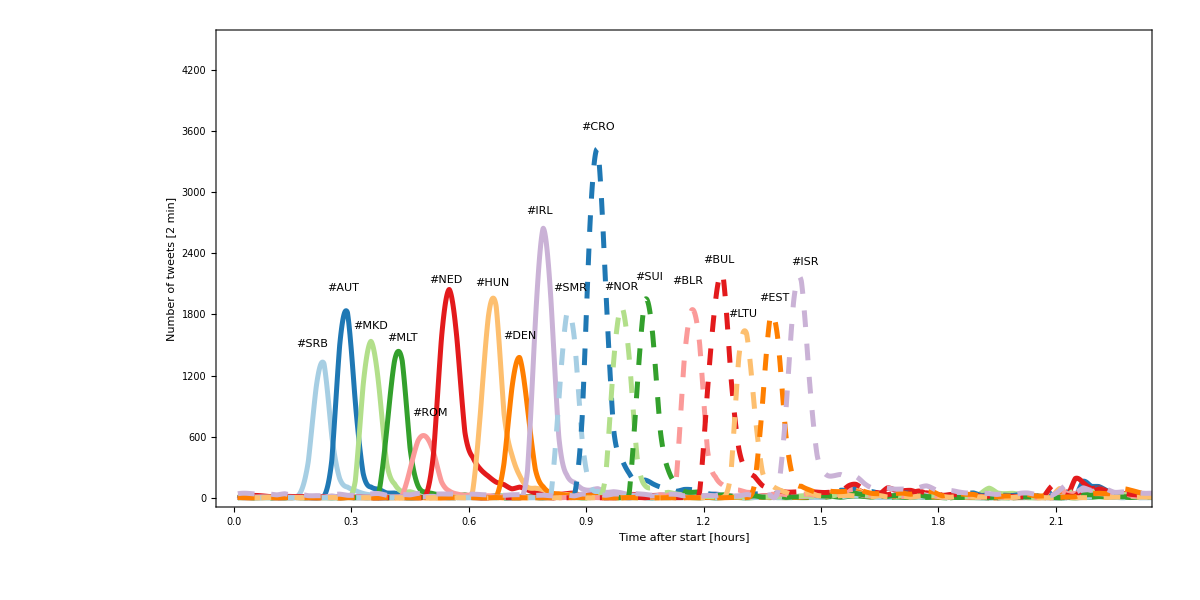

```mathematica
CustomOffset2={{-0.02,0},{0,50},{0.01,-40},{0.01,40},{0.02,40},{0,-100},{0.00,40},{0.01,20},{0,-20},{0.02,70},{0.01,30},{0.01,0},{0.02,40},{0.00,90},{0.00,-30},{0,0},{0.02,0},{0.02,0}}
SF2=Plot[{int[[1]][x],int[[2]][x],int[[3]][x],int[[4]][x],int[[5]][x],int[[6]][x],int[[7]][x],int[[8]][x],int[[9]][x],int[[10]][x],int[[11]][x],int[[12]][x],int[[13]][x],int[[14]][x],int[[15]][x],int[[16]][x],int[[17]][x],int[[18]][x]},{x,0.01,2.5},PlotRange->{{0,2.3},{0,4500}},ImageSize->1200,AspectRatio->1/2,PlotStyle->{{Thickness[0.003],RGBColor[166/255,206/255,227/255]},{Thickness[0.003],RGBColor[31/255,120/255,180/255]},{Thickness[0.003],RGBColor[178/255,223/255,138/255]},{Thickness[0.003],RGBColor[51/255,160/255,44/255]},{Thickness[0.003],RGBColor[251/255,154/255,153/255]},{Thickness[0.003],RGBColor[227/255,26/255,28/255]},{Thickness[0.003],RGBColor[253/255,191/255,111/255]},{Thickness[0.003],RGBColor[255/255,127/255,0/255]},{Thickness[0.003],RGBColor[202/255,178/255,214/255]},{Thickness[0.003],RGBColor[166/255,206/255,227/255],Dashing[0.01]},{Thickness[0.003],RGBColor[31/255,120/255,180/255],Dashing[0.01]},{Thickness[0.003],RGBColor[178/255,223/255,138/255],Dashing[0.01]},{Thickness[0.003],RGBColor[51/255,160/255,44/255],Dashing[0.01]},{Thickness[0.003],RGBColor[251/255,154/255,153/255],Dashing[0.01]},{Thickness[0.003],RGBColor[227/255,26/255,28/255],Dashing[0.01]},{Thickness[0.003],RGBColor[253/255,191/255,111/255],Dashing[0.01]},{Thickness[0.003],RGBColor[255/255,127/255,0/255],Dashing[0.01]},{Thickness[0.003],RGBColor[202/255,178/255,214/255],Dashing[0.01]}},FrameLabel->{"Time after start [hours]","Number of tweets [2 min]","Eurovision 2017, Semi-final 2"},{Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{Black,25,FontFamily->"Helvetica"}},Epilog->Table[Inset[Text[Style[hashtags2[[i]],FontSize->15,Bold,Colors2[[i]]]],{TableOfMax[[i,1]]-0.01+CustomOffset2[[i,1]],190+CustomOffset2[[i,2]]+TableOfMax[[i,2]]}],{i,18}]]
```

## Analysis

Number of tweets per eahc country

```mathematica
NumberOfTweets1={Table[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[i]][[All,1]][[1]],{i,Length[SearchNames]}],Table[Total[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[i]][[All,2]]],{i,Length[SearchNames]}]}//Transpose
NumberOfTweetsWithoutOwn1={NumberOfTweets1[[All,1]],NumberOfTweets1[[All,2]]-Join[Table[DataReduced[[i,3,i,2]],{i,Length[DataReduced]}],ConstantArray[0,42-18]]}//Transpose
```

{{SWEDEN,2746},{GEORGIA,748},{AUSTRALIA,4237},{ALBANIA,86},{BELGIUM,6018},{MONTENEGRO,279},{FINLAND,3663},{AZERBAIJAN,255},{PORTUGAL,7325},{GREECE,2115},{POLAND,2841},{MOLDOVA,83},{ICELAND,906},{CZECH REPUBLIC,352},{CYPRUS,547},{ARMENIA,815},{SLOVENIA,552},{LATVIA,353},{SERBIA,3117},{AUSTRIA,3860},{MACEDONIA,154},{MALTA,88},{ROMANIA,391},{NETHERLANDS,4879},{HUNGARY,493},{DENMARK,4493},{IRELAND,3874},{SAN MARINO,0},{CROATIA,478},{NORWAY,4425},{SWITZERLAND,1160},{BELARUS,572},{BULGARIA,83},{LITHUANIA,270},{ESTONIA,434},{ISRAEL,117},{UKRAINE,666},{FRANCE,2897},{GERMANY,6407},{ITALY,3930},{SPAIN,5637},{UK,18308}}

{{SWEDEN,2253},{GEORGIA,597},{AUSTRALIA,3301},{ALBANIA,34},{BELGIUM,5078},{MONTENEGRO,61},{FINLAND,2945},{AZERBAIJAN,107},{PORTUGAL,1250},{GREECE,1447},{POLAND,2066},{MOLDOVA,41},{ICELAND,712},{CZECH REPUBLIC,326},{CYPRUS,228},{ARMENIA,675},{SLOVENIA,448},{LATVIA,225},{SERBIA,3117},{AUSTRIA,3860},{MACEDONIA,154},{MALTA,88},{ROMANIA,391},{NETHERLANDS,4879},{HUNGARY,493},{DENMARK,4493},{IRELAND,3874},{SAN MARINO,0},{CROATIA,478},{NORWAY,4425},{SWITZERLAND,1160},{BELARUS,572},{BULGARIA,83},{LITHUANIA,270},{ESTONIA,434},{ISRAEL,117},{UKRAINE,666},{FRANCE,2897},{GERMANY,6407},{ITALY,3930},{SPAIN,5637},{UK,18308}}

```mathematica
FirstVoting={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,40,41,42}
NumberOfTweets1[[All,1]][[FirstVoting]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,40,41,42}

{SWEDEN,GEORGIA,AUSTRALIA,ALBANIA,BELGIUM,MONTENEGRO,FINLAND,AZERBAIJAN,PORTUGAL,GREECE,POLAND,MOLDOVA,ICELAND,CZECH REPUBLIC,CYPRUS,ARMENIA,SLOVENIA,LATVIA,ITALY,SPAIN,UK}

```mathematica
NumberOfTweets2={Table[GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[i]][[All,1]][[1]],{i,Length[SearchNames]}],Table[Total[GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[i]][[All,2]]],{i,Length[SearchNames]}]}//Transpose
NumberOfTweetsWithoutOwn2={NumberOfTweets2[[All,1]],NumberOfTweets2[[All,2]]-Join[ConstantArray[0,18],Table[DataReduced2[[i,3,i+18,2]],{i,1,18}],ConstantArray[0,6]]}//Transpose
```

{{SWEDEN,1768},{GEORGIA,358},{AUSTRALIA,2999},{ALBANIA,25},{BELGIUM,3652},{MONTENEGRO,29},{FINLAND,2209},{AZERBAIJAN,53},{PORTUGAL,589},{GREECE,791},{POLAND,1505},{MOLDOVA,55},{ICELAND,448},{CZECH REPUBLIC,240},{CYPRUS,159},{ARMENIA,488},{SLOVENIA,334},{LATVIA,103},{SERBIA,2825},{AUSTRIA,3202},{MACEDONIA,347},{MALTA,430},{ROMANIA,540},{NETHERLANDS,6319},{HUNGARY,591},{DENMARK,4639},{IRELAND,5488},{SAN MARINO,0},{CROATIA,1435},{NORWAY,4187},{SWITZERLAND,1327},{BELARUS,982},{BULGARIA,289},{LITHUANIA,316},{ESTONIA,783},{ISRAEL,564},{UKRAINE,598},{FRANCE,2300},{GERMANY,6295},{ITALY,3724},{SPAIN,4175},{UK,14808}}

{{SWEDEN,1768},{GEORGIA,358},{AUSTRALIA,2999},{ALBANIA,25},{BELGIUM,3652},{MONTENEGRO,29},{FINLAND,2209},{AZERBAIJAN,53},{PORTUGAL,589},{GREECE,791},{POLAND,1505},{MOLDOVA,55},{ICELAND,448},{CZECH REPUBLIC,240},{CYPRUS,159},{ARMENIA,488},{SLOVENIA,334},{LATVIA,103},{SERBIA,2356},{AUSTRIA,2918},{MACEDONIA,100},{MALTA,205},{ROMANIA,411},{NETHERLANDS,4798},{HUNGARY,341},{DENMARK,4302},{IRELAND,4038},{SAN MARINO,0},{CROATIA,648},{NORWAY,3796},{SWITZERLAND,1090},{BELARUS,552},{BULGARIA,83},{LITHUANIA,189},{ESTONIA,382},{ISRAEL,126},{UKRAINE,598},{FRANCE,2300},{GERMANY,6295},{ITALY,3724},{SPAIN,4175},{UK,14808}}

```mathematica
SecondVoting={19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39}
NumberOfTweets2[[All,1]][[SecondVoting]]
```

{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39}

{SERBIA,AUSTRIA,MACEDONIA,MALTA,ROMANIA,NETHERLANDS,HUNGARY,DENMARK,IRELAND,SAN MARINO,CROATIA,NORWAY,SWITZERLAND,BELARUS,BULGARIA,LITHUANIA,ESTONIA,ISRAEL,UKRAINE,FRANCE,GERMANY}

```mathematica
NumberOfTweets={NumberOfTweetsWithoutOwn1[[All,1]],Total[#]&/@Transpose[{NumberOfTweetsWithoutOwn1[[All,2]],NumberOfTweetsWithoutOwn2[[All,2]]}]}//Transpose
```

{{SWEDEN,4021},{GEORGIA,955},{AUSTRALIA,6300},{ALBANIA,59},{BELGIUM,8730},{MONTENEGRO,90},{FINLAND,5154},{AZERBAIJAN,160},{PORTUGAL,1839},{GREECE,2238},{POLAND,3571},{MOLDOVA,96},{ICELAND,1160},{CZECH REPUBLIC,566},{CYPRUS,387},{ARMENIA,1163},{SLOVENIA,782},{LATVIA,328},{SERBIA,5473},{AUSTRIA,6778},{MACEDONIA,254},{MALTA,293},{ROMANIA,802},{NETHERLANDS,9677},{HUNGARY,834},{DENMARK,8795},{IRELAND,7912},{SAN MARINO,0},{CROATIA,1126},{NORWAY,8221},{SWITZERLAND,2250},{BELARUS,1124},{BULGARIA,166},{LITHUANIA,459},{ESTONIA,816},{ISRAEL,243},{UKRAINE,1264},{FRANCE,5197},{GERMANY,12702},{ITALY,7654},{SPAIN,9812},{UK,33116}}

Get all tweets from a single country, select on the end only those which voted in this semi

```mathematica
FirstVoting
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,37,38,41}

```mathematica
FirstVotingModifiedForSanMarino={1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,37,38,40,41};
```

```mathematica
Fractions1=Join[Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3],#[[3]]≠hashtags[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}}],Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,19,42}]][[FirstVoting]];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Fractions2=Join[Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,1,18}],Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3],#[[3]]≠hashtagsall[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,19,36}],Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,37,42}]][[SecondVoting]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{SERBIA,93,#AUT,0.0169925},{SERBIA,113,#MKD,0.0206468},{SERBIA,77,#MLT,0.0140691},{SERBIA,63,#ROM,0.0115111},{SERBIA,128,#NED,0.0233875},{SERBIA,176,#HUN,0.0321579},{SERBIA,126,#DEN,0.0230221},{SERBIA,164,#IRL,0.0299653},{SERBIA,92,#SMR,0.0168098},{SERBIA,297,#CRO,0.0542664},{SERBIA,101,#NOR,0.0184542},{SERBIA,122,#SUI,0.0222912},{SERBIA,99,#BLR,0.0180888},{SERBIA,177,#BUL,0.0323406},{SERBIA,87,#LTU,0.0158962},{SERBIA,125,#EST,0.0228394},{SERBIA,316,#ISR,0.057738}},{{AUSTRIA,110,#SRB,0.016229},{AUSTRIA,120,#MKD,0.0177043},{AUSTRIA,107,#MLT,0.0157864},{AUSTRIA,79,#ROM,0.0116554},{AUSTRIA,186,#NED,0.0274417},{AUSTRIA,177,#HUN,0.0261139},{AUSTRIA,184,#DEN,0.0271467},{AUSTRIA,171,#IRL,0.0252287},{AUSTRIA,158,#SMR,0.0233107},{AUSTRIA,338,#CRO,0.0498672},{AUSTRIA,173,#NOR,0.0255238},{AUSTRIA,168,#SUI,0.0247861},{AUSTRIA,147,#BLR,0.0216878},{AUSTRIA,187,#BUL,0.0275893},{AUSTRIA,137,#LTU,0.0202125},{AUSTRIA,177,#EST,0.0261139},{AUSTRIA,299,#ISR,0.0441133}},{{MACEDONIA,9,#SRB,0.0354331},{MACEDONIA,2,#AUT,0.00787402},{MACEDONIA,0,#MLT,0.},{MACEDONIA,2,#ROM,0.00787402},{MACEDONIA,4,#NED,0.015748},{MACEDONIA,12,#HUN,0.0472441},{MACEDONIA,5,#DEN,0.019685},{MACEDONIA,4,#IRL,0.015748},{MACEDONIA,5,#SMR,0.019685},{MACEDONIA,21,#CRO,0.0826772},{MACEDONIA,3,#NOR,0.011811},{MACEDONIA,3,#SUI,0.011811},{MACEDONIA,6,#BLR,0.023622},{MACEDONIA,15,#BUL,0.0590551},{MACEDONIA,1,#LTU,0.00393701},{MACEDONIA,2,#EST,0.00787402},{MACEDONIA,6,#ISR,0.023622}},{{MALTA,11,#SRB,0.0375427},{MALTA,13,#AUT,0.0443686},{MALTA,10,#MKD,0.0341297},{MALTA,4,#ROM,0.0136519},{MALTA,14,#NED,0.0477816},{MALTA,15,#HUN,0.0511945},{MALTA,13,#DEN,0.0443686},{MALTA,21,#IRL,0.0716724},{MALTA,11,#SMR,0.0375427},{MALTA,23,#CRO,0.0784983},{MALTA,13,#NOR,0.0443686},{MALTA,9,#SUI,0.0307167},{MALTA,7,#BLR,0.0238908},{MALTA,14,#BUL,0.0477816},{MALTA,9,#LTU,0.0307167},{MALTA,6,#EST,0.0204778},{MALTA,12,#ISR,0.0409556}},{{ROMANIA,14,#SRB,0.0174564},{ROMANIA,23,#AUT,0.0286783},{ROMANIA,13,#MKD,0.0162095},{ROMANIA,13,#MLT,0.0162095},{ROMANIA,26,#NED,0.032419},{ROMANIA,46,#HUN,0.0573566},{ROMANIA,19,#DEN,0.0236908},{ROMANIA,26,#IRL,0.032419},{ROMANIA,14,#SMR,0.0174564},{ROMANIA,37,#CRO,0.0461347},{ROMANIA,22,#NOR,0.0274314},{ROMANIA,24,#SUI,0.0299252},{ROMANIA,20,#BLR,0.0249377},{ROMANIA,48,#BUL,0.0598504},{ROMANIA,16,#LTU,0.0199501},{ROMANIA,13,#EST,0.0162095},{ROMANIA,37,#ISR,0.0461347}},{{NETHERLANDS,171,#SRB,0.0176708},{NETHERLANDS,301,#AUT,0.0311047},{NETHERLANDS,238,#MKD,0.0245944},{NETHERLANDS,239,#MLT,0.0246977},{NETHERLANDS,110,#ROM,0.0113672},{NETHERLANDS,297,#HUN,0.0306913},{NETHERLANDS,209,#DEN,0.0215976},{NETHERLANDS,403,#IRL,0.0416451},{NETHERLANDS,225,#SMR,0.023251},{NETHERLANDS,511,#CRO,0.0528056},{NETHERLANDS,325,#NOR,0.0335848},{NETHERLANDS,327,#SUI,0.0337915},{NETHERLANDS,258,#BLR,0.0266612},{NETHERLANDS,343,#BUL,0.0354449},{NETHERLANDS,264,#LTU,0.0272812},{NETHERLANDS,253,#EST,0.0261445},{NETHERLANDS,324,#ISR,0.0334815}},{{HUNGARY,13,#SRB,0.0155875},{HUNGARY,20,#AUT,0.0239808},{HUNGARY,26,#MKD,0.0311751},{HUNGARY,12,#MLT,0.0143885},{HUNGARY,6,#ROM,0.00719424},{HUNGARY,27,#NED,0.0323741},{HUNGARY,11,#DEN,0.0131894},{HUNGARY,19,#IRL,0.0227818},{HUNGARY,12,#SMR,0.0143885},{HUNGARY,33,#CRO,0.0395683},{HUNGARY,23,#NOR,0.0275779},{HUNGARY,22,#SUI,0.0263789},{HUNGARY,21,#BLR,0.0251799},{HUNGARY,33,#BUL,0.0395683},{HUNGARY,14,#LTU,0.0167866},{HUNGARY,22,#EST,0.0263789},{HUNGARY,27,#ISR,0.0323741}},{{DENMARK,159,#SRB,0.0180785},{DENMARK,254,#AUT,0.02888},{DENMARK,168,#MKD,0.0191018},{DENMARK,188,#MLT,0.0213758},{DENMARK,121,#ROM,0.0137578},{DENMARK,261,#NED,0.029676},{DENMARK,297,#HUN,0.0337692},{DENMARK,350,#IRL,0.0397953},{DENMARK,246,#SMR,0.0279704},{DENMARK,409,#CRO,0.0465037},{DENMARK,237,#NOR,0.0269471},{DENMARK,243,#SUI,0.0276293},{DENMARK,220,#BLR,0.0250142},{DENMARK,330,#BUL,0.0375213},{DENMARK,163,#LTU,0.0185333},{DENMARK,263,#EST,0.0299034},{DENMARK,393,#ISR,0.0446845}},{{IRELAND,153,#SRB,0.0193377},{IRELAND,200,#AUT,0.0252781},{IRELAND,180,#MKD,0.0227503},{IRELAND,165,#MLT,0.0208544},{IRELAND,140,#ROM,0.0176946},{IRELAND,318,#NED,0.0401921},{IRELAND,242,#HUN,0.0305865},{IRELAND,148,#DEN,0.0187058},{IRELAND,167,#SMR,0.0211072},{IRELAND,579,#CRO,0.07318},{IRELAND,266,#NOR,0.0336198},{IRELAND,233,#SUI,0.0294489},{IRELAND,179,#BLR,0.0226239},{IRELAND,306,#BUL,0.0386754},{IRELAND,167,#LTU,0.0211072},{IRELAND,232,#EST,0.0293225},{IRELAND,363,#ISR,0.0458797}},{{SAN MARINO,0,#SRB,Indeterminate},{SAN MARINO,0,#AUT,Indeterminate},{SAN MARINO,0,#MKD,Indeterminate},{SAN MARINO,0,#MLT,Indeterminate},{SAN MARINO,0,#ROM,Indeterminate},{SAN MARINO,0,#NED,Indeterminate},{SAN MARINO,0,#HUN,Indeterminate},{SAN MARINO,0,#DEN,Indeterminate},{SAN MARINO,0,#IRL,Indeterminate},{SAN MARINO,0,#CRO,Indeterminate},{SAN MARINO,0,#NOR,Indeterminate},{SAN MARINO,0,#SUI,Indeterminate},{SAN MARINO,0,#BLR,Indeterminate},{SAN MARINO,0,#BUL,Indeterminate},{SAN MARINO,0,#LTU,Indeterminate},{SAN MARINO,0,#EST,Indeterminate},{SAN MARINO,0,#ISR,Indeterminate}},{{CROATIA,40,#SRB,0.035524},{CROATIA,35,#AUT,0.0310835},{CROATIA,48,#MKD,0.0426288},{CROATIA,13,#MLT,0.0115453},{CROATIA,22,#ROM,0.0195382},{CROATIA,44,#NED,0.0390764},{CROATIA,58,#HUN,0.0515098},{CROATIA,32,#DEN,0.0284192},{CROATIA,43,#IRL,0.0381883},{CROATIA,32,#SMR,0.0284192},{CROATIA,31,#NOR,0.0275311},{CROATIA,27,#SUI,0.0239787},{CROATIA,37,#BLR,0.0328597},{CROATIA,62,#BUL,0.0550622},{CROATIA,29,#LTU,0.0257549},{CROATIA,41,#EST,0.0364121},{CROATIA,54,#ISR,0.0479574}},{{NORWAY,147,#SRB,0.017881},{NORWAY,200,#AUT,0.0243279},{NORWAY,179,#MKD,0.0217735},{NORWAY,339,#MLT,0.0412359},{NORWAY,84,#ROM,0.0102177},{NORWAY,264,#NED,0.0321129},{NORWAY,228,#HUN,0.0277339},{NORWAY,178,#DEN,0.0216519},{NORWAY,269,#IRL,0.0327211},{NORWAY,155,#SMR,0.0188542},{NORWAY,377,#CRO,0.0458582},{NORWAY,214,#SUI,0.0260309},{NORWAY,225,#BLR,0.0273689},{NORWAY,296,#BUL,0.0360054},{NORWAY,147,#LTU,0.017881},{NORWAY,182,#EST,0.0221384},{NORWAY,312,#ISR,0.0379516}},{{SWITZERLAND,40,#SRB,0.0177778},{SWITZERLAND,57,#AUT,0.0253333},{SWITZERLAND,49,#MKD,0.0217778},{SWITZERLAND,41,#MLT,0.0182222},{SWITZERLAND,22,#ROM,0.00977778},{SWITZERLAND,93,#NED,0.0413333},{SWITZERLAND,62,#HUN,0.0275556},{SWITZERLAND,49,#DEN,0.0217778},{SWITZERLAND,77,#IRL,0.0342222},{SWITZERLAND,59,#SMR,0.0262222},{SWITZERLAND,107,#CRO,0.0475556},{SWITZERLAND,59,#NOR,0.0262222},{SWITZERLAND,73,#BLR,0.0324444},{SWITZERLAND,88,#BUL,0.0391111},{SWITZERLAND,60,#LTU,0.0266667},{SWITZERLAND,72,#EST,0.032},{SWITZERLAND,82,#ISR,0.0364444}},{{BELARUS,27,#SRB,0.0240214},{BELARUS,29,#AUT,0.0258007},{BELARUS,29,#MKD,0.0258007},{BELARUS,26,#MLT,0.0231317},{BELARUS,10,#ROM,0.0088968},{BELARUS,31,#NED,0.0275801},{BELARUS,47,#HUN,0.0418149},{BELARUS,25,#DEN,0.022242},{BELARUS,45,#IRL,0.0400356},{BELARUS,19,#SMR,0.0169039},{BELARUS,53,#CRO,0.047153},{BELARUS,40,#NOR,0.0355872},{BELARUS,31,#SUI,0.0275801},{BELARUS,55,#BUL,0.0489324},{BELARUS,22,#LTU,0.019573},{BELARUS,27,#EST,0.0240214},{BELARUS,36,#ISR,0.0320285}},{{BULGARIA,0,#SRB,0.},{BULGARIA,4,#AUT,0.0240964},{BULGARIA,8,#MKD,0.0481928},{BULGARIA,0,#MLT,0.},{BULGARIA,5,#ROM,0.0301205},{BULGARIA,5,#NED,0.0301205},{BULGARIA,11,#HUN,0.0662651},{BULGARIA,6,#DEN,0.0361446},{BULGARIA,6,#IRL,0.0361446},{BULGARIA,1,#SMR,0.0060241},{BULGARIA,11,#CRO,0.0662651},{BULGARIA,6,#NOR,0.0361446},{BULGARIA,1,#SUI,0.0060241},{BULGARIA,4,#BLR,0.0240964},{BULGARIA,4,#LTU,0.0240964},{BULGARIA,4,#EST,0.0240964},{BULGARIA,7,#ISR,0.0421687}},{{LITHUANIA,5,#SRB,0.0108932},{LITHUANIA,11,#AUT,0.0239651},{LITHUANIA,8,#MKD,0.0174292},{LITHUANIA,5,#MLT,0.0108932},{LITHUANIA,9,#ROM,0.0196078},{LITHUANIA,10,#NED,0.0217865},{LITHUANIA,14,#HUN,0.0305011},{LITHUANIA,5,#DEN,0.0108932},{LITHUANIA,10,#IRL,0.0217865},{LITHUANIA,4,#SMR,0.0087146},{LITHUANIA,22,#CRO,0.0479303},{LITHUANIA,25,#NOR,0.0544662},{LITHUANIA,8,#SUI,0.0174292},{LITHUANIA,7,#BLR,0.0152505},{LITHUANIA,26,#BUL,0.0566449},{LITHUANIA,12,#EST,0.0261438},{LITHUANIA,8,#ISR,0.0174292}},{{ESTONIA,8,#SRB,0.00980392},{ESTONIA,22,#AUT,0.0269608},{ESTONIA,11,#MKD,0.0134804},{ESTONIA,11,#MLT,0.0134804},{ESTONIA,12,#ROM,0.0147059},{ESTONIA,14,#NED,0.0171569},{ESTONIA,37,#HUN,0.0453431},{ESTONIA,14,#DEN,0.0171569},{ESTONIA,37,#IRL,0.0453431},{ESTONIA,18,#SMR,0.0220588},{ESTONIA,44,#CRO,0.0539216},{ESTONIA,25,#NOR,0.0306373},{ESTONIA,13,#SUI,0.0159314},{ESTONIA,29,#BLR,0.0355392},{ESTONIA,40,#BUL,0.0490196},{ESTONIA,25,#LTU,0.0306373},{ESTONIA,22,#ISR,0.0269608}},{{ISRAEL,4,#SRB,0.0164609},{ISRAEL,10,#AUT,0.0411523},{ISRAEL,6,#MKD,0.0246914},{ISRAEL,5,#MLT,0.0205761},{ISRAEL,5,#ROM,0.0205761},{ISRAEL,8,#NED,0.0329218},{ISRAEL,11,#HUN,0.0452675},{ISRAEL,4,#DEN,0.0164609},{ISRAEL,8,#IRL,0.0329218},{ISRAEL,5,#SMR,0.0205761},{ISRAEL,9,#CRO,0.037037},{ISRAEL,10,#NOR,0.0411523},{ISRAEL,7,#SUI,0.0288066},{ISRAEL,14,#BLR,0.0576132},{ISRAEL,7,#BUL,0.0288066},{ISRAEL,3,#LTU,0.0123457},{ISRAEL,10,#EST,0.0411523}},{{UKRAINE,21,#SRB,0.0166139},{UKRAINE,36,#AUT,0.028481},{UKRAINE,30,#MKD,0.0237342},{UKRAINE,22,#MLT,0.0174051},{UKRAINE,14,#ROM,0.0110759},{UKRAINE,24,#NED,0.0189873},{UKRAINE,23,#HUN,0.0181962},{UKRAINE,23,#DEN,0.0181962},{UKRAINE,34,#IRL,0.0268987},{UKRAINE,11,#SMR,0.00870253},{UKRAINE,35,#CRO,0.0276899},{UKRAINE,34,#NOR,0.0268987},{UKRAINE,31,#SUI,0.0245253},{UKRAINE,68,#BLR,0.0537975},{UKRAINE,60,#BUL,0.0474684},{UKRAINE,24,#LTU,0.0189873},{UKRAINE,53,#EST,0.0419304},{UKRAINE,55,#ISR,0.0435127}},{{FRANCE,62,#SRB,0.01193},{FRANCE,114,#AUT,0.0219357},{FRANCE,121,#MKD,0.0232827},{FRANCE,70,#MLT,0.0134693},{FRANCE,67,#ROM,0.0128921},{FRANCE,120,#NED,0.0230902},{FRANCE,166,#HUN,0.0319415},{FRANCE,104,#DEN,0.0200115},{FRANCE,166,#IRL,0.0319415},{FRANCE,102,#SMR,0.0196267},{FRANCE,213,#CRO,0.0409852},{FRANCE,112,#NOR,0.0215509},{FRANCE,119,#SUI,0.0228978},{FRANCE,124,#BLR,0.0238599},{FRANCE,135,#BUL,0.0259765},{FRANCE,76,#LTU,0.0146238},{FRANCE,136,#EST,0.0261689},{FRANCE,293,#ISR,0.0563787}},{{GERMANY,212,#SRB,0.0166903},{GERMANY,381,#AUT,0.0299953},{GERMANY,258,#MKD,0.0203118},{GERMANY,244,#MLT,0.0192096},{GERMANY,144,#ROM,0.0113368},{GERMANY,391,#NED,0.0307826},{GERMANY,430,#HUN,0.0338529},{GERMANY,312,#DEN,0.0245631},{GERMANY,462,#IRL,0.0363722},{GERMANY,331,#SMR,0.0260589},{GERMANY,560,#CRO,0.0440875},{GERMANY,333,#NOR,0.0262163},{GERMANY,332,#SUI,0.0261376},{GERMANY,333,#BLR,0.0262163},{GERMANY,466,#BUL,0.0366871},{GERMANY,225,#LTU,0.0177137},{GERMANY,362,#EST,0.0284994},{GERMANY,519,#ISR,0.0408597}}}

```mathematica
(*Subsituting San marino with Italy*)
```

```mathematica
Table[Fractions2[[10]][[j,2]]=Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,{40}}][[1]][[All,2]][[j]],{j,17}];
Table[Fractions2[[10]][[j,4]]=Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,{40}}][[1]][[All,4]][[j]],{j,17}];
```